```mathematica
TickListLeft={};
TickListRight={};
For[j=-15,j≤1,j++,TickListLeft=Append[TickListLeft,{j,If[j≠ 0,Superscript[10,j],1],{0.02,0}}];
TickListRight=Append[TickListRight,{j,"",{0.02,0}}];
For[k=2,k≤9,k++,TickListLeft=Append[TickListLeft,{j+Log[10,k],"",{0.01,0}}];
TickListRight=Append[TickListRight,{j+Log[10,k],"",{0.01,0}}];]]
```

```mathematica
TickListBottom={};
TickListTop={};
For[j=0,j≤7,j++,TickListBottom=Append[TickListBottom,{j,Superscript[10,j],{0.02,0}}];
TickListTop=Append[TickListTop,{j,"",{0.02,0}}];
For[k=2,k≤9,k++,TickListBottom=Append[TickListBottom,{j+Log[10,k],"",{0.01,0}}];
TickListTop=Append[TickListTop,{j+Log[10,k],"",{0.01,0}}];]]

EmptyPlot=RegionPlot[0>1,{lMA,1,3},{lgA,-2,0},PlotRange->{{1,3},{-2,0}},PlotPoints->50,FrameTicks->{{TickListLeft,TickListRight},{TickListBottom,TickListTop}},LabelStyle->Larger,FrameLabel->{"m_χ [GeV]","α"},FrameStyle->Thickness[0.003]]
```

-Graphics-

```mathematica
InvGev3tocm2g = 2184 10^(-7);
kmsToSpeedOfLight = 3336*10^(-9);
```

```mathematica
s[b_] := Piecewise[{{2 Pi b^2 Log[1 + b^(-2)],b < 10^(-2)},{7 Pi (b^(1.8) + 280 (b/10)^10.3)/(1+ 1.4 b + 0.006 b^4 +160 ( b/10)^10),10^(-2) ≤ b ≤ 10^2},{0.81 Pi (1 + Log[b] - 1/(2 Log[b]))^2,b>10^2}}]
```

```mathematica
σTmχ[v_,mχ_,mp_,α_]:=InvGev3tocm2g/mχ*s[2 α mp /(mχ (kmsToSpeedOfLight *v)^2)]/mp^2
```

```mathematica
σTmχavg[mχ_?NumericQ,mp_?NumericQ,α_?NumericQ,vm_?NumericQ] := 4*Pi/(Sqrt[2 Pi]vm)^3 NIntegrate[v^2 Exp[-v^2/(2vm^2)] σTmχ[v,mχ,mp,α],{v,0,vm*30},MaxRecursion->20,WorkingPrecision->7]
```

```mathematica
FixmpCluster[mχ_,α_]:=Max[10^lmp,10^-30]/.FindRoot[σTmχ[2000,mχ,10^lmp,α]==0.2,{lmp,Log[10,mχ]-5}]
FixmpDwarf[mχ_,α_]:=Max[10^lmp,10^-30]/.FindRoot[σTmχ[50,mχ,10^lmp,α]==5,{lmp,Log[10,mχ]-5}]
```

```mathematica
T1=Flatten[Parallelize[Table[{lmx,la,FixmpCluster[10^lmx,10^la]},{lmx,0,5,0.1},{la,-3,0,0.1}]],1]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{0.,-3.,0.176957},{0.,-2.9,0.195372},{0.,-2.8,0.216086},{0.,-2.7,0.227595},{0.,-2.6,0.237569},{0.,-2.5,0.247534},{0.,-2.4,0.257823},{0.,-2.3,0.26852},{0.,-2.2,0.279657},1563,{5.,-0.8,1.},{5.,-0.7,1.},{5.,-0.6,1.},{5.,-0.5,1.},{5.,-0.4,1.},{5.,-0.3,1.},{5.,-0.2,1.},{5.,-0.1,1.},{5.,0.,1.}}
 |  |  |  |

```mathematica
I1=Interpolation[T1,InterpolationOrder->1];
```

```mathematica
T2=Flatten[Parallelize[Table[{lmx,la,FixmpDwarf[10^lmx,10^la]},{lmx,0,5,0.1},{la,-3,0,0.1}]],1]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{0.,-3.,0.103987},{0.,-2.9,0.106703},{0.,-2.8,0.10941},{0.,-2.7,0.11211},{0.,-2.6,0.114801},{0.,-2.5,0.117486},{0.,-2.4,0.120163},{0.,-2.3,0.122835},1565,{5.,-0.7,1/1000000000000000000000000000000},{5.,-0.6,1/1000000000000000000000000000000},{5.,-0.5,1/1000000000000000000000000000000},{5.,-0.4,1/1000000000000000000000000000000},{5.,-0.3,1/1000000000000000000000000000000},{5.,-0.2,1/1000000000000000000000000000000},{5.,-0.1,1/1000000000000000000000000000000},{5.,0.,1/1000000000000000000000000000000}}
 |  |  |  |

```mathematica
I2=Interpolation[T2,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
T3=Flatten[Parallelize[Table[{lmx,la,Log[10,σTmχ[50,10^lmx,I1[lmx,la],10^la]]},{lmx,0,5,0.1},{la,-3,0,0.1}]],1]
```

{{0.,-3.,0.283058},{0.,-2.9,0.224291},{0.,-2.8,0.163286},{0.,-2.7,0.140195},{0.,-2.6,0.123697},{0.,-2.5,0.108141},{0.,-2.4,0.0924169},{0.,-2.3,0.0763125},{0.,-2.2,0.0598011},1563,{5.,-0.8,-6.7541},{5.,-0.7,-6.71855},{5.,-0.6,-6.68447},{5.,-0.5,-6.65173},{5.,-0.4,-6.62022},{5.,-0.3,-6.58985},{5.,-0.2,-6.56054},{5.,-0.1,-6.53221},{5.,0.,-6.5048}}
 |  |  |  |

```mathematica
I3=Interpolation[T3,InterpolationOrder->1];
```

```mathematica
P1=ContourPlot[{I1[x,y]==4*10^-3,I1[x,y]==7*10^-3,I1[x,y]==10*10^-3},{x,1,3},{y,-2,0},Contours->{2,5,10}*10^-3,ContourStyle->{{ColorData[97][1],DotDashed},{ColorData[97][1],Dashed},{ColorData[97][1],Dotted}}];
```

```mathematica
P2a=RegionPlot[{0>1,I3[x,y]>1.3,I3[x,y]<0.3},{x,1,3},{y,-2,0}];
P2b=RegionPlot[{I1[x,y]/10^x>50*kmsToSpeedOfLight},{x,1,3},{y,-2,0},BoundaryStyle->Gray,PlotStyle->LightGray];
```

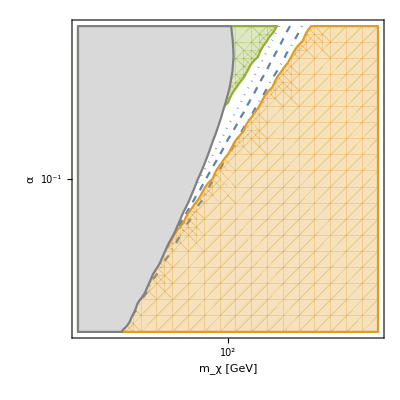

```mathematica
Plot1=Show[EmptyPlot,P1,P2a,P2b]
```

```mathematica
T4=Flatten[Parallelize[Table[{lmx,la,Log[10,σTmχ[2000,10^lmx,I2[lmx,la],10^la]]},{lmx,0,5,0.1},{la,-3,0,0.1}]],1]
```

{{0.,-3.,-0.164684},{0.,-2.9,-0.209672},{0.,-2.8,-0.280487},{0.,-2.7,-0.251602},{0.,-2.6,-0.187654},{0.,-2.5,-0.155278},{0.,-2.4,-0.136861},{0.,-2.3,-0.121902},{0.,-2.2,-0.107479},{0.,-2.1,-0.0928994},1562,{5.,-0.8,-8.00086},{5.,-0.7,-7.80226},{5.,-0.6,-7.60366},{5.,-0.5,-7.40507},{5.,-0.4,-7.20648},{5.,-0.3,-7.00789},{5.,-0.2,-6.80931},{5.,-0.1,-6.61073},{5.,0.,-6.41216}}
 |  |  |  |

```mathematica
I4=Interpolation[T4,InterpolationOrder->1];
```

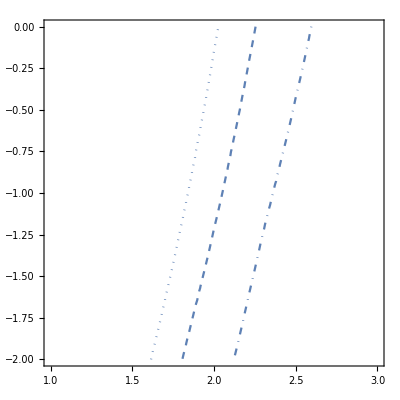

```mathematica
P3=ContourPlot[{I2[x,y]==4*10^-3,I2[x,y]==7*10^-3,I2[x,y]==10*10^-3},{x,1,3},{y,-2,0},Contours->{2,5,10}*10^-3,ContourStyle->{{ColorData[97][1],DotDashed},{ColorData[97][1],Dashed},{ColorData[97][1],Dotted}}]
```

```mathematica
P4a=RegionPlot[{0>1,I4[x,y]>-0.5,I4[x,y]<-1},{x,1,3},{y,-2,0}];
P4b=RegionPlot[{I2[x,y]/10^x>50*kmsToSpeedOfLight},{x,1,3},{y,-2,0},BoundaryStyle->Gray,PlotStyle->LightGray];
```

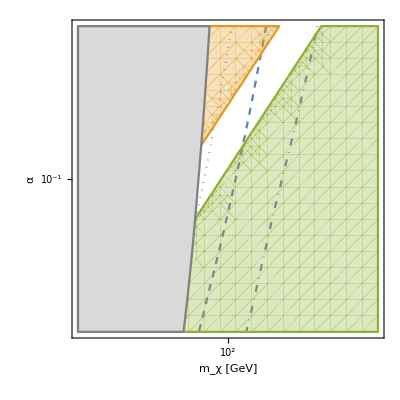

```mathematica
Plot2=Show[EmptyPlot,P3,P4a,P4b]
```

```mathematica
Export[NotebookDirectory[]<>"sigma_dwarf.pdf",Plot1]
Export[NotebookDirectory[]<>"sigma_cluster.pdf",Plot2]
```